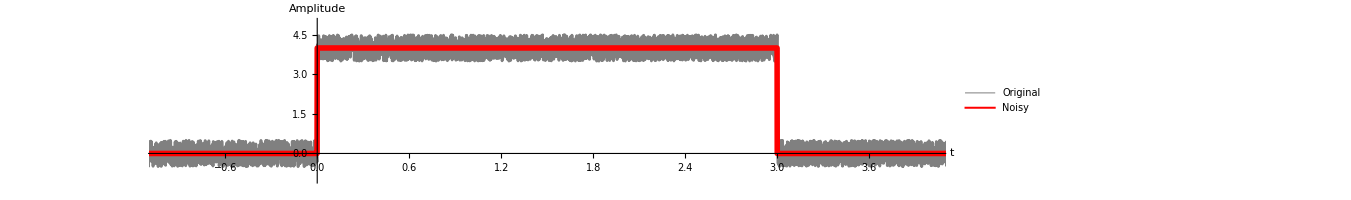

```mathematica
(*Окно, чтобы показать исходный и шумный сигнал*)
a=4;
t1=0;
t2=3;
c=0;
d=5;
b=0.5;

T=20;
dt=0.001;
tValues=Range[-T/2,T/2,dt];
n=Length[tValues];

vValues=Table[-1/(2 dt)+(k-1)*1/T,{k,n}];

gVals=Table[If[t1<=t<=t2,a,0],{t,tValues}];
xi=RandomReal[{-1,1},n];
uVals=gVals+b*xi+c*Sin[d*tValues];

ListLinePlot[{Transpose[{tValues,uVals}], Transpose[{tValues,gVals}]}, 
AspectRatio->0.2,
PlotLegends->Placed[{"Original", "Noisy"},Right],
 PlotStyle->{{Gray,Thickness[0.002]},{Red, Thickness[0.004]}},
AxesLabel->{"t","Amplitude"},
ImageSize->1000,
PlotRange->{{-1, 4},{-1,5}}
]
```

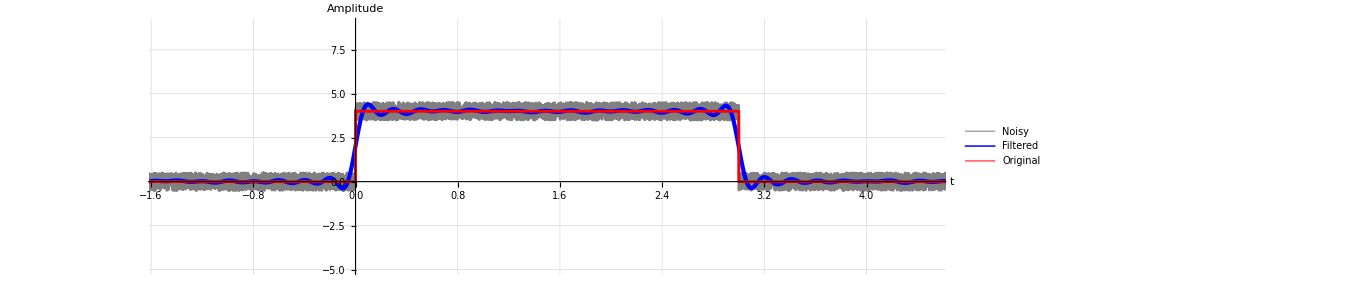

```mathematica
(*Фильтрация [-v; v]]*)
v=5;
U=Fourier[uVals,FourierParameters->{1,-1}];
Ushifted=RotateLeft[U,Floor[n/2]];  

filterMask=Table[If[Abs[f]<=v,1,0],{f,vValues}];
Ufiltered=Ushifted*filterMask; 
UfilteredBack=RotateRight[Ufiltered,Floor[n/2]];
uFilteredVals=InverseFourier[UfilteredBack,FourierParameters->{1,-1}];

ListLinePlot[{Transpose[{tValues,uVals}],Transpose[{tValues,Re[uFilteredVals]}], Transpose[{tValues, gVals}]},
PlotStyle->{{Gray,Thickness[0.002]},{Blue,Thickness[0.003]}, {Red, Thickness[0.002]}},
AxesLabel->{"t","Amplitude"},
PlotLegends->Placed[{"Noisy","Filtered", "Original"},Right],
AspectRatio->0.3,
ImageSize->1000,
PlotRange->{{-1.5, 4.5},{-5,9}}, 
GridLines->Automatic
]
```

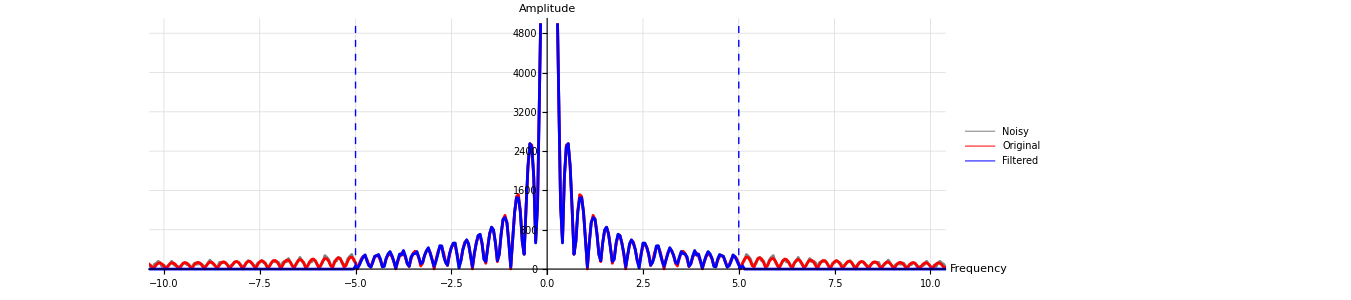

```mathematica
(*Фурье-образы + отрисовка*)
G=Fourier[gVals,FourierParameters->{1,-1}];
Gshifted=RotateLeft[G,Floor[n/2]];

UfilteredSpec=Fourier[Re[uFilteredVals],FourierParameters->{1,-1}];
UfilteredShifted=RotateLeft[UfilteredSpec,Floor[n/2]];

vidthN = 5000;

ListLinePlot[{Transpose[{vValues,Abs[Ushifted]}],Transpose[{vValues,Abs[Gshifted]}],Transpose[{vValues,Abs[UfilteredShifted]}]},PlotStyle->{{Gray,Thickness[0.002]},{Red,Thickness[0.002]},{Blue,Thickness[0.002]}},
AxesLabel->{"Frequency","Amplitude"},
PlotLegends->Placed[{"Noisy","Original","Filtered"},Right],
AspectRatio->0.3,
ImageSize->1000,
PlotRange->{{-10,10},{-10,vidthN}}, 
Epilog->{
Dashed,Blue,
Line[{{v,0},{v,vidthN}}],
Line[{{-v,0},{-v,vidthN}}]
},
GridLines->Automatic
]
```